```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Ed\GitHub\Wavelets

```mathematica
grid0 = Transpose[Import["grid0.csv"]][[1]];
grid1 = Transpose[Import["grid1.csv"]][[1]];
grid2 = Transpose[Import["grid2.csv"]][[1]];
grid3 = Transpose[Import["grid3.csv"]][[1]];
```

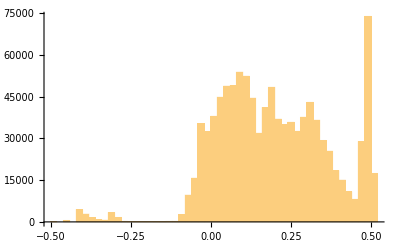

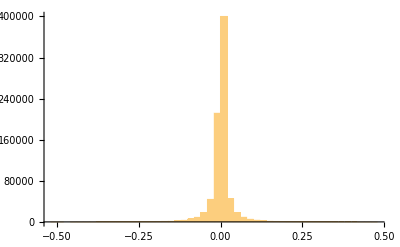

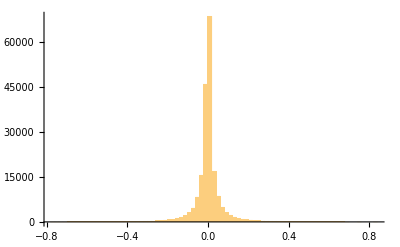

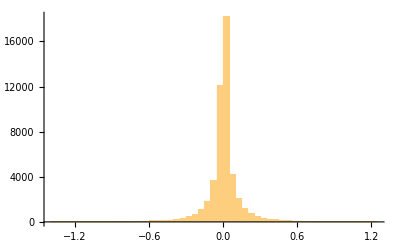

```mathematica
Histogram[grid0, 50]
Histogram[grid1, 50]
Histogram[grid2, 50]
Histogram[grid3, 50]
```

```mathematica
grid01 = Transpose[Import["grid0_01.csv"]][[1]];
grid10 = Transpose[Import["grid0_10.csv"]][[1]];
grid11 = Transpose[Import["grid0_11.csv"]][[1]];
```

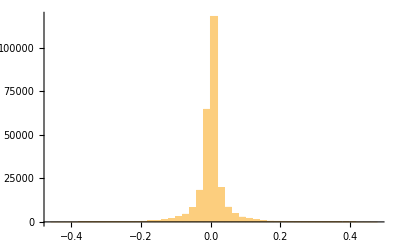

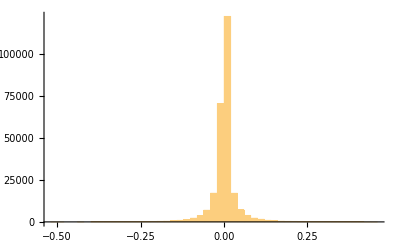

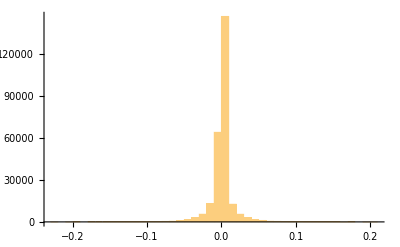

```mathematica
Histogram[grid01, 50]
Histogram[grid10, 50]
Histogram[grid11, 50]
```

```mathematica
grid02 = Transpose[Import["grid1_01.csv"]][[1]];
grid20 = Transpose[Import["grid1_10.csv"]][[1]];
grid22 = Transpose[Import["grid1_11.csv"]][[1]];
```

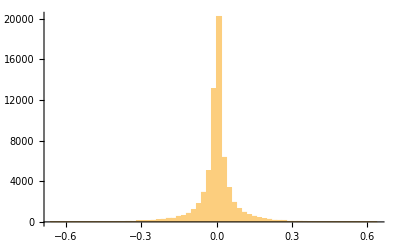

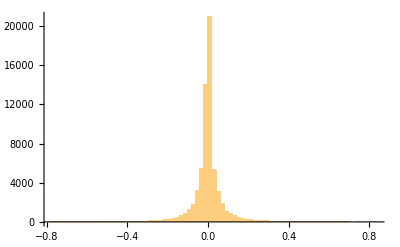

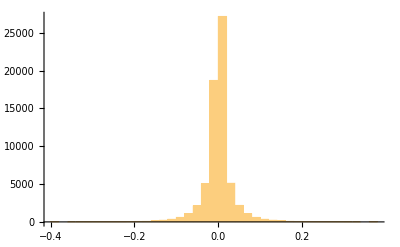

```mathematica
Histogram[grid02, 50]
Histogram[grid20, 50]
Histogram[grid22, 50]
```

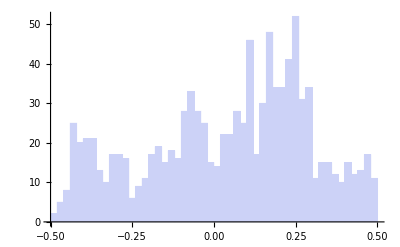

```mathematica
myNorm[x_] := 0.26210966 x + -0.39669812;
Histogram[myNorm /@ grid0, 50]
```

1024

1.67206

1.

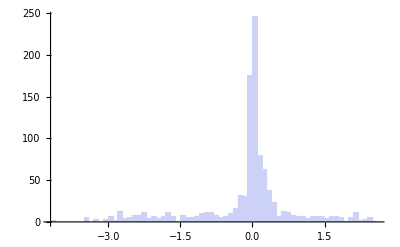

```mathematica
len = Length[grid0]
avg=(Plus@@grid0)/len
myNorm[x_] :=   (x-avg)^3 / 2.11614
StandardDeviation[myNorm /@ grid0]
Histogram[myNorm /@ grid0, 50]
```

```mathematica
cor = Transpose[Import["bqsmall.csv"]][[1]];
```

```mathematica
corlog = Log[Abs[#]]& /@ cor;
```

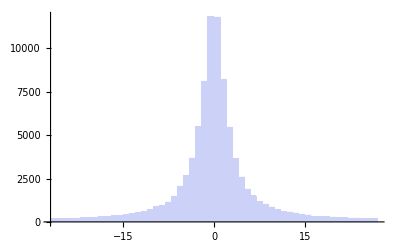

```mathematica
Histogram[Select[cor, Abs[#] < 27 &], 37]
```

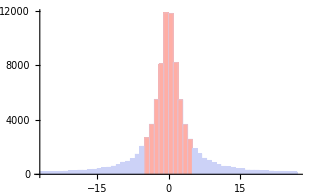

```mathematica
lenna = Transpose[Import["bqlenna.csv"]][[1]];
```

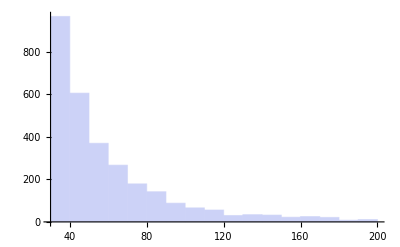

```mathematica
Histogram[Select[lenna, #<200 &]]
```

```mathematica
?Histogram
```

Histogram[{x_1,x_2,…}] plots a histogram of the values x_i.
Histogram[{x_1,x_2,…},bspec] plots a histogram with bin width specification bspec.
Histogram[{x_1,x_2,…},bspec,hspec] plots a histogram with bin heights computed according to the specification hspec.
Histogram[{data_1,data_2,…},…] plots histograms for multiple datasets data_i.

```mathematica
(* ./test_compress_cpu -bq bqlenna.cube -steps 4,4 -thresh .95 -qcount 20 -qalg lloyd-err lenna.cube out.cube *)
```

```mathematica
distpoints = Import["bqlenna_rand.tsv"];
```

```mathematica
distpoints[[2]]
```

{30.8624,0.375406}

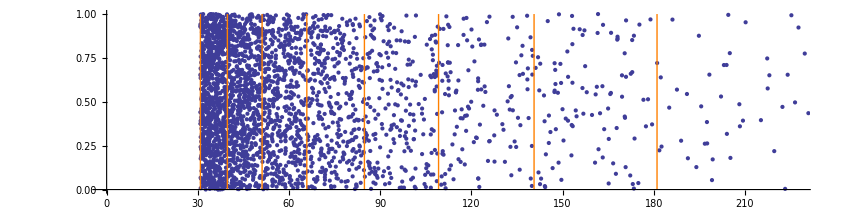

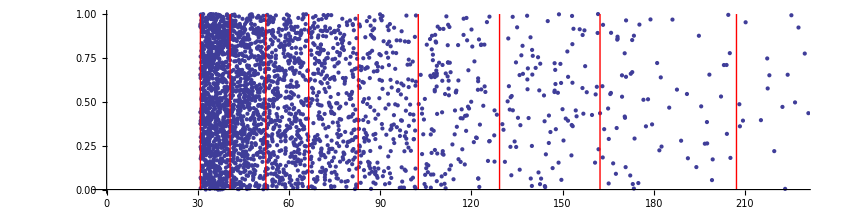

```mathematica
(* Log *)
ListPlot[distpoints,AspectRatio->1/4,
AxesStyle->FontSize->Larger,
Epilog->{Thick, Orange,
Line[{{30.8475,0},{30.8475,1}}],
Line[{{39.7219,0},{39.7219,1}}],
Line[{{51.1493,0},{51.1493,1}}],
Line[{{65.8643,0},{65.8643,1}}],
Line[{{84.8125,0},{84.8125,1}}],
Line[{{109.212,0},{109.212,1}}],
Line[{{140.631,0},{140.631,1}}],
Line[{{181.088,0},{181.088,1}}],
Line[{{233.185,0},{233.185,1}}]
}]

(* Lloyd *)
ListPlot[distpoints,AspectRatio->1/4,
AxesStyle->FontSize->Larger,
Epilog->{Thick, Red,
Line[{{30.8475,0},{30.8475,1}}],Line[{{40.6204,0},{40.6204,1}}],Line[{{52.3915,0},{52.3915,1}}],Line[{{66.4799,0},{66.4799,1}}],Line[{{82.7671,0},{82.7671,1}}],Line[{{102.535,0},{102.535,1}}],Line[{{129.275,0},{129.275,1}}],Line[{{162.331,0},{162.331,1}}],Line[{{207.228,0},{207.228,1}}],Line[{{267.03,0},{267.03,1}}]
}]
```

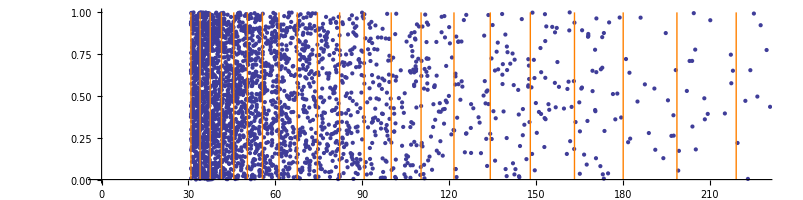

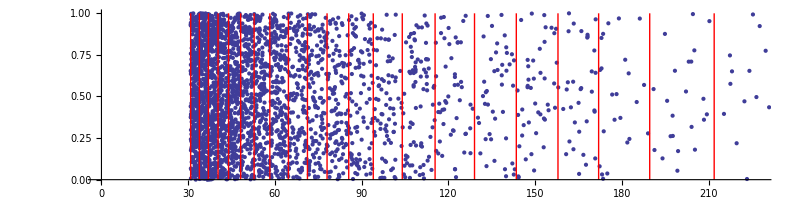

```mathematica
(* Log, pSNR 28.946 *)
ListPlot[distpoints,AspectRatio->1/4,
AxesStyle->FontSize->Larger,
Epilog->{Thick, Orange,
Line[{{30.8475,0},{30.8475,1}}],Line[{{34.0251,0},{34.0251,1}}],Line[{{37.53,0},{37.53,1}}],Line[{{41.3959,0},{41.3959,1}}],Line[{{45.6601,0},{45.6601,1}}],Line[{{50.3636,0},{50.3636,1}}],Line[{{55.5515,0},{55.5515,1}}],Line[{{61.2739,0},{61.2739,1}}],Line[{{67.5857,0},{67.5857,1}}],Line[{{74.5477,0},{74.5477,1}}],Line[{{82.2269,0},{82.2269,1}}],Line[{{90.6971,0},{90.6971,1}}],Line[{{100.04,0},{100.04,1}}],Line[{{110.345,0},{110.345,1}}],Line[{{121.711,0},{121.711,1}}],Line[{{134.249,0},{134.249,1}}],Line[{{148.078,0},{148.078,1}}],Line[{{163.331,0},{163.331,1}}],Line[{{180.156,0},{180.156,1}}],Line[{{198.714,0},{198.714,1}}],Line[{{219.184,0},{219.184,1}}],Line[{{241.762,0},{241.762,1}}],Line[{{266.666,0},{266.666,1}}]
}]

(* Lloyd, pSNR 29.384 *)
ListPlot[distpoints,AspectRatio->1/4,
AxesStyle->FontSize->Larger,
Epilog->{Thick, Red,
Line[{{30.8475,0},{30.8475,1}}],Line[{{33.8701,0},{33.8701,1}}],Line[{{36.9853,0},{36.9853,1}}],Line[{{40.3272,0},{40.3272,1}}],Line[{{43.9507,0},{43.9507,1}}],Line[{{48.1402,0},{48.1402,1}}],Line[{{52.7942,0},{52.7942,1}}],Line[{{58.2331,0},{58.2331,1}}],Line[{{64.6595,0},{64.6595,1}}],Line[{{71.2316,0},{71.2316,1}}],Line[{{78.0153,0},{78.0153,1}}],Line[{{85.5084,0},{85.5084,1}}],Line[{{93.9983,0},{93.9983,1}}],Line[{{104.028,0},{104.028,1}}],Line[{{115.374,0},{115.374,1}}],Line[{{129.008,0},{129.008,1}}],Line[{{143.462,0},{143.462,1}}],Line[{{157.872,0},{157.872,1}}],Line[{{171.931,0},{171.931,1}}],Line[{{189.596,0},{189.596,1}}],Line[{{211.887,0},{211.887,1}}],Line[{{232.258,0},{232.258,1}}],Line[{{253.056,0},{253.056,1}}]
}]
```